## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d03_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
json="/Volumes/home/BEM/benchmark20250220/Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float/result.json"
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d03_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
jsonInfo[json]
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

/Volumes/home/BEM/benchmark20250220/Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float/result.json

no. | title | length
1 | cpu_time | 702
2 | eq_of_motion | 702
3 | gauge0_intersection | 702
4 | gauge1_intersection | 702
5 | gauge2_intersection | 702
6 | gauge3_intersection | 702
7 | gauge4_intersection | 702
8 | gauge5_intersection | 702
9 | gauge6_intersection | 702
10 | gauge7_intersection | 702
11 | gauge8_intersection | 702
12 | gauge9_intersection | 702
13 | gradPhi_worst_grad | 702
14 | gradPhi_worst_iteration | 702
15 | gradPhi_worst_value | 702
16 | simulation_time | 702
17 | wall_clock_time | 702
18 | water_E | 702
19 | water_EK | 702
20 | water_EP | 702
21 | water_face_size | 702
22 | water_point_size | 702
23 | water_volume | 702

```mathematica
gauge1EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
gauge2EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
gauge3EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];

h=0.25;
shiftt=4.88;
ListPlot[
{{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge3_intersection",3]-h)*100}ᵀ,
}
,GridLines->Automatic
,ImageSize->Large
,PlotRange->{{0,15},{-0.2,4}}
,Evaluate[plot2Doption]]
```

```mathematica
gauge1EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
gauge2EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
gauge3EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];

h=0.25;
shiftt=4.88;
ListPlot[
{(*{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[json,"simulation_time"]-shiftt,(importData[json,"gauge3_intersection",3]-h)*100}ᵀ,*)
gauge1EXP,
gauge2EXP,
gauge3EXP}
,GridLines->Automatic
,ImageSize->Large
,PlotRange->{{0,15},{-0.2,4}}
,Evaluate[plot2Doption]]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/Goring1979Gauge1.csvが見付かりませんでした．

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/Goring1979Gauge2.csvが見付かりませんでした．

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/Goring1979Gauge3.csvが見付かりませんでした．

-Graphics-

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

```mathematica
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
```

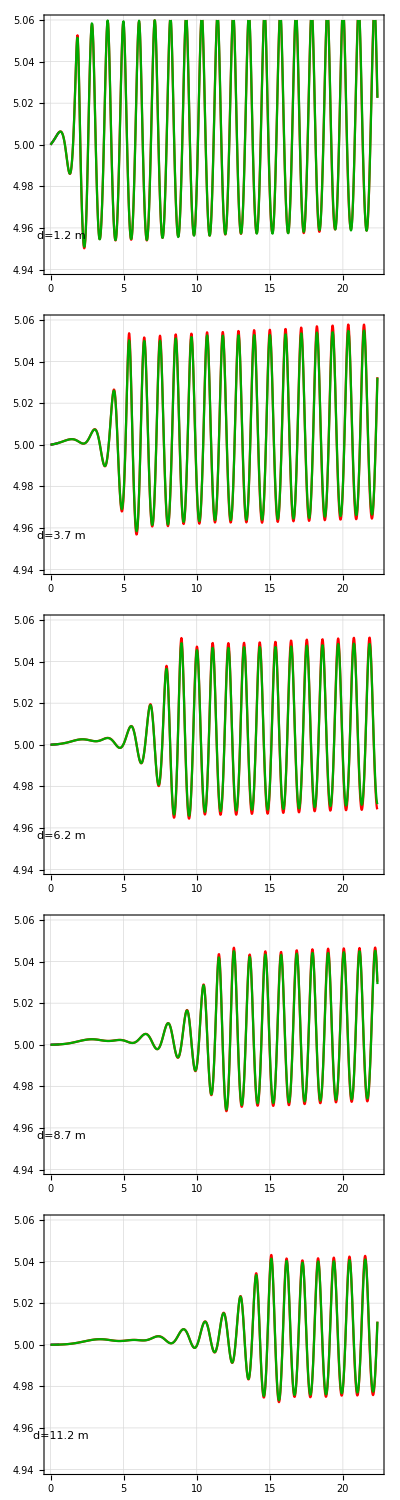
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

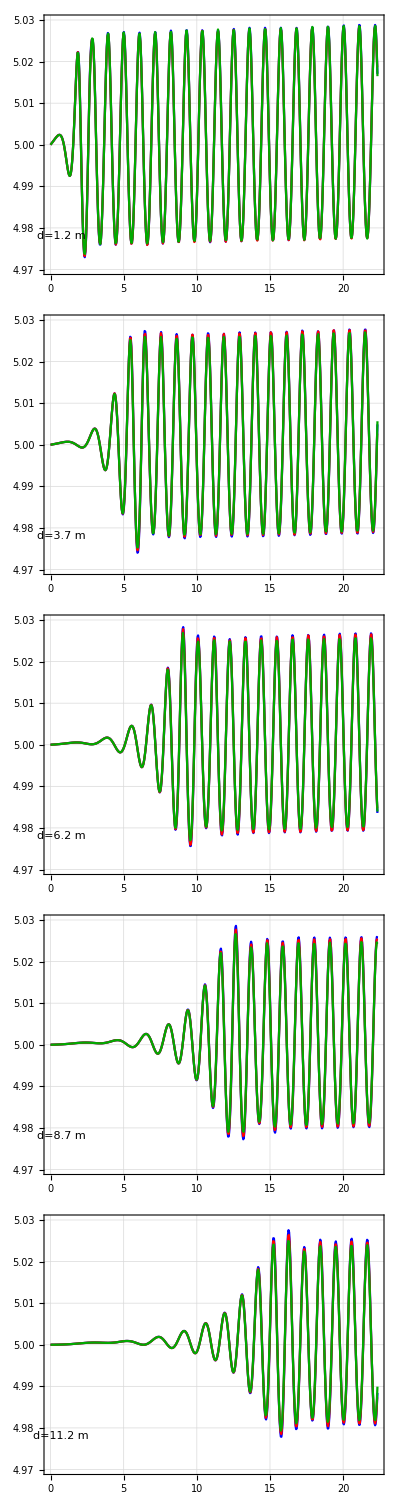
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)

comp0d08={
"/Volumes/home/BEM/benchmark20250220/Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float/result.json",
"/Volumes/home/BEM/benchmark20250220/Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float/result.json"};
fig=compareSimple[fileDir&/@comp0d08,zrange]
(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->300]*)

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->300]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```